```mathematica
Dd[n_,0,a_]:=1;Dd[n_,1,a_]:=Floor[n]-a+1
Dd[n_,k_,a_]:=Dd[n,k,a]=Sum[Binomial[k,j] Dd[n/(m^(k-j)),j,m+1],{m,a,n^(1/k)},{j,0,k-1}]
P2[n_,j_]:= P2[n,j]=Sum[1/k!(D[Log[1+x]^j,{x,k}]/.x->0) Dd[n,k,2],{k,0,Log[2,n]}]
DAlt[x_,z_]:=Sum[z^k/k! P2[x,k],{k,0,Log[2,x]}]
cs[ x_, z_] := Sum[(D[ Cos[r],{r,k}]/.r->0)/k! P2[x,k],{k,0,Log[2,x]}]
sn[ x_, z_] := Sum[(D[Sin[r],{r,k}]/.r->0)/k! P2[x,k],{k,0,Log[2,x]}]
cssq[ x_, z_] := Sum[(D[ Cos[r]^2,{r,k}]/.r->0)/k! P2[x,k],{k,0,Log[2,x]}]
snsq[ x_, z_] := Sum[(D[Sin[r]^2,{r,k}]/.r->0)/k! P2[x,k],{k,0,Log[2,x]}]

DAlt[ 100,I]
```

-2881/72+(65 ⅈ)/8

```mathematica
D[ Cos[ x],{x,6}]/.x->0
```

-1

```mathematica
cs[100,1]+I sn[100,1]
```

-2881/72+(65 ⅈ)/8

```mathematica
cssq[100,1]+ snsq[100,1]
```

1

```mathematica
DAlt[100,x]
```

1+(428 x)/15+(16289 x^2)/360+(331 x^3)/16+(611 x^4)/144+(67 x^5)/240+(7 x^6)/720

```mathematica
ddd[ n_, r_,j_, c_ ]:= DAlt[ n, r(Cos[ 2Pi j / c]+ I Sin[ 2Pi j/c])]
ddd2[ n_, r_,j_, c_ ]:= (DAlt[ n, r(Cos[ 2Pi j / c]+ I Sin[ 2Pi j/c])]-1)/(r(Cos[ 2Pi j / c]+ I Sin[ 2Pi j/c]))
ff[ n_, r_, c_] := Sum[(1/c) DAlt[ n, r(Cos[ 2Pi j / c]+ I Sin[ 2Pi j/c])],{j,0,c-1}]
ffp[ n_, r_, c_] := Sum[(1/c) ddd2[n,r,j,c],{j,0,c-1}]
ff2[ n_, r_, c_] := DiscretePlot[{Re[ ddd2[n,r,j,c]], Im[ ddd2[n,r,j,c]]},{j,0,c-1}]
ffa[ n_, r_, c_] := DiscretePlot[{Re[ ddd[n,r,j,c]], Im[ ddd[n,r,j,c]]},{j,0,c-1}]
ffb[ n_, r_, c_] := DiscretePlot[{Abs[ ddd[n,r,j,c]]},{j,0,c-1}]
```

```mathematica
ffp[100,1,4.]
```

28.8125+1.77636×10^-15 ⅈ

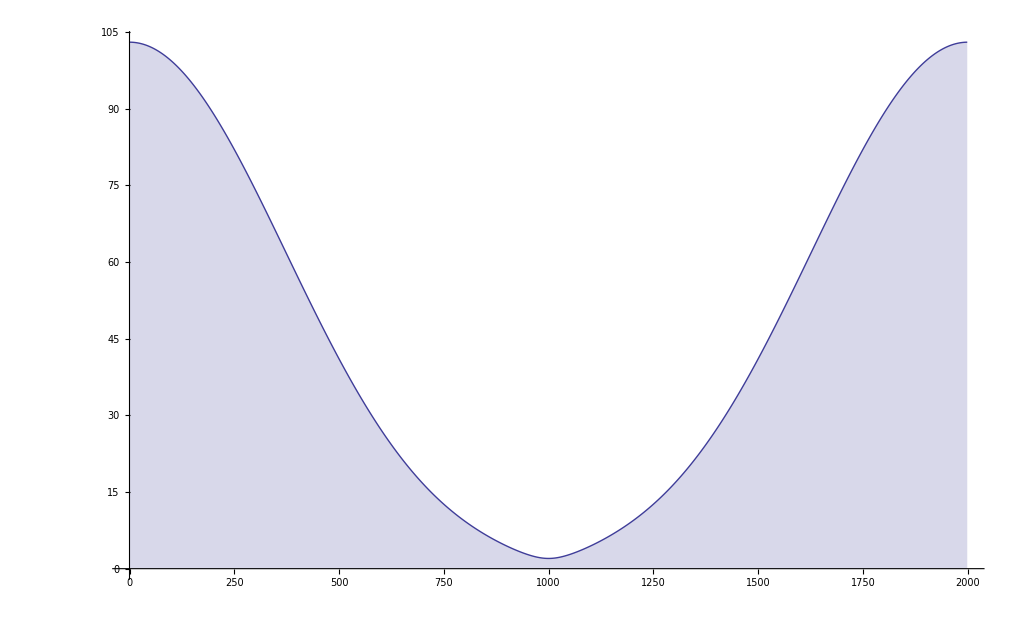

```mathematica
ffb[103,1,2000.]
```

```mathematica
DAlt[100000, z]
```

1+(991892879 z)/102960+(16611877533197 z^2)/605404800+(27613425421567 z^3)/864864000+(8883298064606291 z^4)/435891456000+(82938597121 z^5)/10264320+(12123475378339 z^6)/5748019200+(987114594581 z^7)/2612736000+(6832898553167 z^8)/146313216000+(53237749 z^9)/13063680+(1772592397 z^10)/7315660800+(20466961 z^11)/2052864000+(30323737 z^12)/114960384000+(841 z^13)/186810624+(9773 z^14)/209227898880+(71 z^15)/373621248000+(17 z^16)/20922789888000

```mathematica
1+(991892879 z)/102960+(16611877533197 z^2)/605404800+(27613425421567 z^3)/864864000+(8883298064606291 z^4)/435891456000+(82938597121 z^5)/10264320+(12123475378339 z^6)/5748019200+(987114594581 z^7)/2612736000+(6832898553167 z^8)/146313216000+(53237749 z^9)/13063680+(1772592397 z^10)/7315660800+(20466961 z^11)/2052864000+(30323737 z^12)/114960384000+(841 z^13)/186810624+(9773 z^14)/209227898880+(71 z^15)/373621248000+(17 z^16)/20922789888000/.z->I
```

-7340179524487/804722688-(209626633781 ⅈ)/14370048

```mathematica
DAlt[100,I]
```

-2881/72+(65 ⅈ)/8

```mathematica
Integrate[ E^z ,{z,0,1}]
```

-1+ⅇ

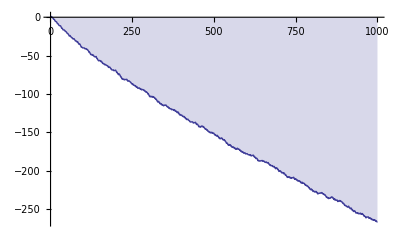

```mathematica
DiscretePlot[ Re[ DAlt[ n, -I]],{n,1,1000}]
```

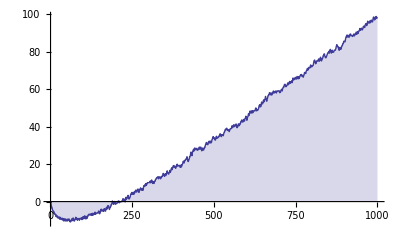

```mathematica
DiscretePlot[ Im[ DAlt[ n, -I]],{n,1,1000}]
```

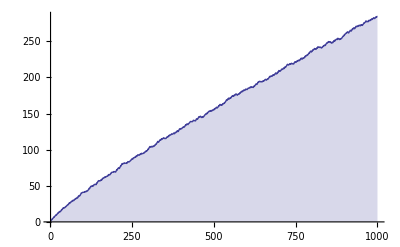

```mathematica
DiscretePlot[ Abs[ DAlt[ n, -I]],{n,1,1000}]
```